# Math

## Basics

### Input

```mathematica
1+2+3
```

6

```mathematica
%+4
```

10

```mathematica
((5-3)^(1+2))/4
```

2

```mathematica
GCD[12,15]
```

3

(Use CTRL+ / to enter fractions.)

```mathematica
1/4+1/3
```

7/12

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
N[1/4+1/7]
```

0.392857

```mathematica
N[1/4+1/7,10]
```

0.3928571429

```mathematica
ScientificForm[0.0001245]
```

1.245×10^-4

```mathematica
N[100!]
```

9.33262×10^157

```mathematica
a1/2
```

a1/2

```mathematica
ab+5xx
```

ab+5 xx

```mathematica
ab+5x x
```

ab+5 x^2

```mathematica
1+2 x/.x->2
```

5

```mathematica
f[x_]:=1+2x
```

```mathematica
f[2]
```

5

## Algebra

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

```mathematica
2+2==4
```

True

```mathematica
1+z==15
```

1+z==15

```mathematica
Solve[x^2+5x-6==0,x]
```

{{x→-6},{x→1}}

```mathematica
NSolve[7 x^2+3x-5==0,x]
```

{{x→-1.08618},{x→0.657611}}

```mathematica
Solve[{x^2+5==y,7x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

```mathematica
Roots[x^2+3x-4==0,x]
```

x==-4||x==1

```mathematica
NRoots[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

x==-1.79025||x==-0.498678||x==0.797819||x==1.68398||x==15.0071

The Reduce command reduces a set of inequalities into a simple form:

```mathematica
Reduce[{0<x<2,1≤x≤4},x]
```

1≤x<2

```mathematica
Reduce[(x-1) (x-2) (x-3) (x-4)>0,x]
```

x<1||2<x<3||x>4

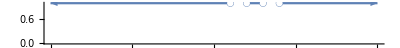

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

### Plot in 2D

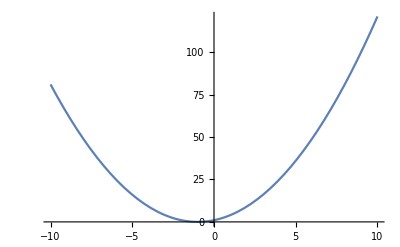

```mathematica
Plot[x^2+2x+1,{x,-10,10}]
```

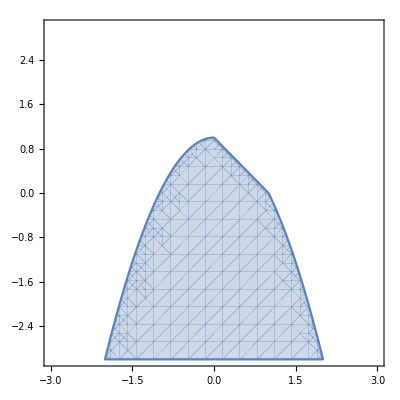

```mathematica
RegionPlot[Reduce[{x^2+y<1&&x+y<1}],{x,-3,3},{y,-3,3}]
```

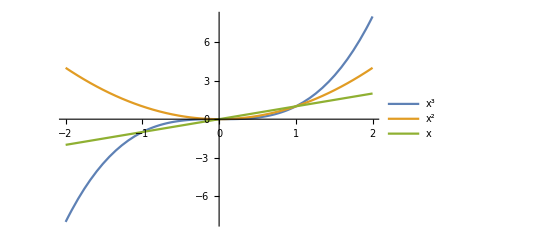

```mathematica
Plot[{x^3,x^2,x},{x,-2,2},PlotLegends->"Expressions"]
```

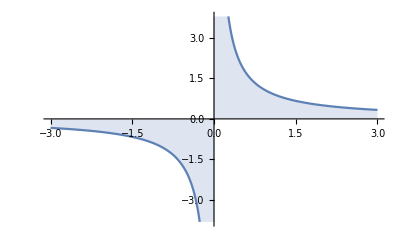

```mathematica
Plot[1/x,{x,-3,3},Filling->Axis]
```

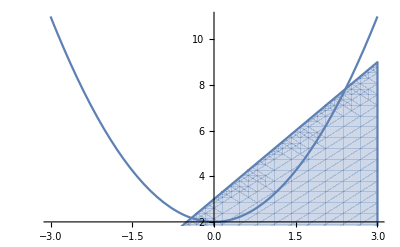

```mathematica
Show[{Plot[x^2+2,{x,-3,3}],RegionPlot[2x>y-3,{x,-3,3},{y,0,9}]}]
```

### Geometry



```mathematica
Graphics[Disk[]]
```

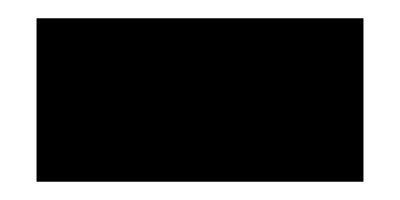

```mathematica
Graphics[Rectangle[{0,0},{4,2}]]
```

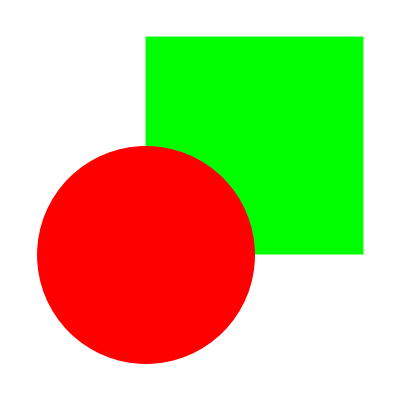

```mathematica
Graphics[{Green,Rectangle[{0,0},{2,2}],Red,Disk[]}]
```

```mathematica
tr = SASTriangle[1,90°,2]
```

Triangle[{{0,0},{√5,0},{4/(√5),2/(√5)}}]

```mathematica
Area[tr]
```

1

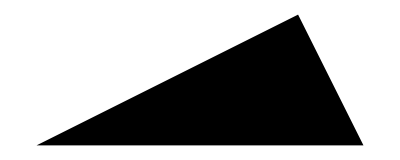

```mathematica
Graphics[tr]
```

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

```mathematica
Volume[Cylinder[]]
```

2 π

```mathematica
Entity["Solid","Ball"][EntityProperty["Solid","Volume"]]
```

Function[a,(4 π a^3)/3]

```mathematica
Entity["Surface","ConeFinite"][EntityProperty["Surface","Volume"]]
```

Function[{a,h},1/3 h π a^2]

```mathematica
Graphics[Rotate[Rectangle[],45°]]
```

-Graphics-

## Trigonometry

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

```mathematica
ArcTan[1]
```

π/4

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[90°]
```

1

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigFactor[Cos[x]^2-Sin[x]^2]
```

2 Sin[π/4-x] Sin[π/4+x]

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

```mathematica
Solve[{Tan[x]==1,0<x<2π}]
```

{{x→π/4},{x→(5 π)/4}}

### Polar Coordinates

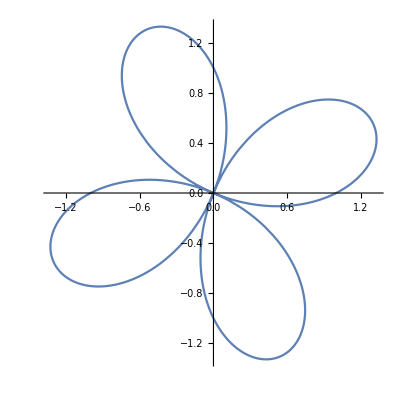

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ],{θ,0,2π}]
```

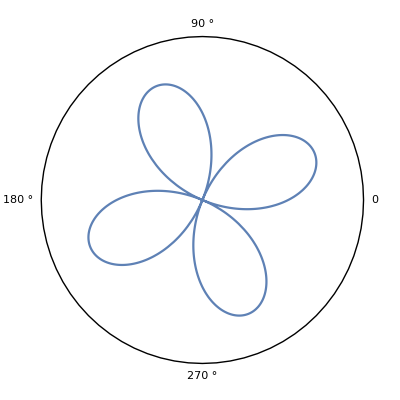

```mathematica
PolarPlot[Sin[2 θ]+Cos[2 θ],{θ,0,2 Pi},PolarAxes->Automatic,PolarTicks->{0 °,90 °,180 °,270 °}]
```

```mathematica
ToPolarCoordinates[{1,1}]
```

{√2,π/4}

### Exponentials & Logarithms

```mathematica
Log[E^2]
```

2

```mathematica
Log[2,64]
```

6

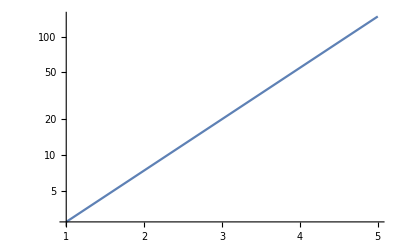

```mathematica
LogPlot[E^x,{x,1,5}]
```

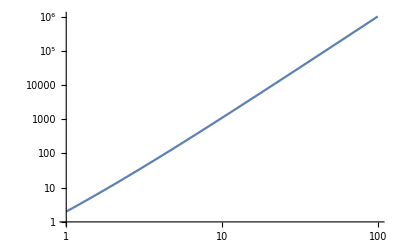

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

### Limit

```mathematica
Limit[(x^2-1)/(x-1),x->1]
```

2

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x-> ∞]
```

2/5

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
TraditionalForm[HoldForm[Limit[1/x,x->∞]]]
```

1/xx∞

### Derivatives

```mathematica
D[x^6,x]
```

6 x^5

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
f[x_]:=x^2+2x+1;
f'[x]
```

2+2 x

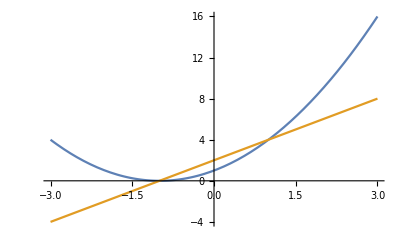

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

```mathematica
D[x^6,{x,3}]
```

120 x^3

```mathematica
Sin''[x]
```

-Sin[x]

```mathematica
Entity["FamousMathProblem","ProductRule"][EntityProperty["FamousMathProblem","AssociatedEquations"]]
```

{d/dx(f(x) g(x)) == f(x) g'(x) + g(x) f'(x)}

### Integrals

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3x]^2,{x,0,π}]
```

28.1531

### Sequences, Sums & Series

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

```mathematica
Table[Fibonacci[x],{x,1,7}]
```

{1,1,2,3,5,8,13}

```mathematica
RecurrenceTable[{a[x]==2a[x-1],a[1]==1},a,{x,1,8}]
```

{1,2,4,8,16,32,64,128}

```mathematica
Total[%]
```

255

```mathematica
Sum[i(i+1),{i,1,10}]
```

440

```mathematica
∑_(i=1)^10 i(i+1)
```

440

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

```mathematica
Series[Exp[x^2],{x,0,8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

```mathematica
Normal[%]
```

1+x^2+x^4/2+x^6/6+x^8/24

```mathematica
Series[2g[x]-3,{x,0,3}]
```

(-3+2 g[0])+2 g'[0] x+g''[0] x^2+1/3 g^(3)[0] x^3+O[x]^4

### Advance Plot 2D

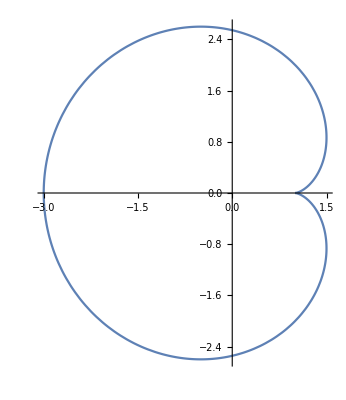

```mathematica
ParametricPlot[{2 Cos[t]-Cos[2t],2Sin[t]-Sin[2t]},{t,0,2π}]
```

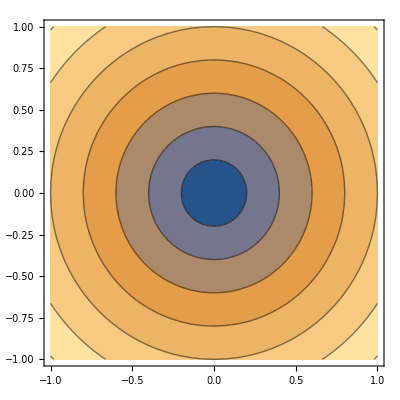

```mathematica
ContourPlot[√(x^2+y^2), {x,-1,1},{y,-1,1}]
```

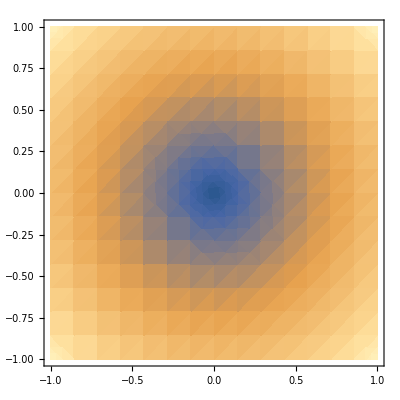

```mathematica
DensityPlot[√(x^2+y^2),{x,-1,1},{y,-1,1}]
```

### Plot 3D

```mathematica
Plot3D[x^2-y^2,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

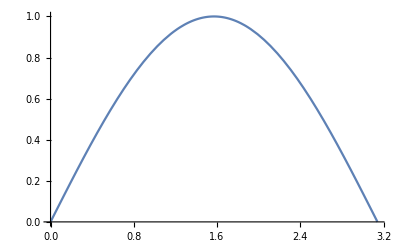

```mathematica
Plot[Sin[θ],{θ,0,π}]
```

```mathematica
RevolutionPlot3D[x^4-x^2,{x,-1,1}]
```

-Graphics3D-

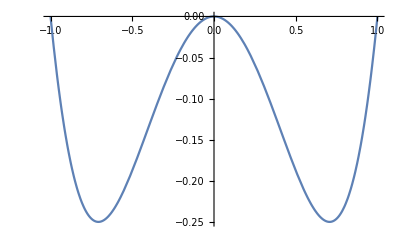

```mathematica
Plot[x^4-x^2,{x,-1,1}]
```

### Multivariate Calculates

```mathematica
D[x^3 z+2 y^2 x+y z^3,y,z]
```

3 z^2

```mathematica
D[(x^2-2x y+x y z), x,y]
```

-2+z

```mathematica
∫∫∫(x^2+y^2+z^2)ⅆyⅆxⅆz
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

```mathematica
Simplify[1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3]
```

1/3 x y z (x^2+y^2+z^2)

```mathematica
∫_-1^1 ∫_-2^x (x Sin[y^2]+y Cos[x^2])ⅆyⅆx
```

1/4 (2 Cos[1]+√(2 π) (-9 FresnelC[√(2/π)]+FresnelS[√(2/π)])+2 Sin[1])

```mathematica
N[%,5]
```

-3.2243

### Vector Analysis & Visualization

```mathematica
{1,2,3}.{a,b,c}
```

a+2 b+3 c

```mathematica
{1,2,3}×{a,b,c}
```

{-3 b+2 c,3 a-c,-2 a+b}

```mathematica
Norm[{1,1,1}]
```

√3

```mathematica
Projection[{8,6,7},{1,0,0}]
```

{8,0,0}

```mathematica
VectorAngle[{1,0},{0,1}]
```

π/2

```mathematica
∇_{x,y} {x^2+y,x+y^2}
```

{{2 x,1},{1,2 y}}

```mathematica
MatrixForm[{{2 x,1},{1,2 y}}]
```

(2 x | 1
1 | 2 y)

```mathematica
Div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

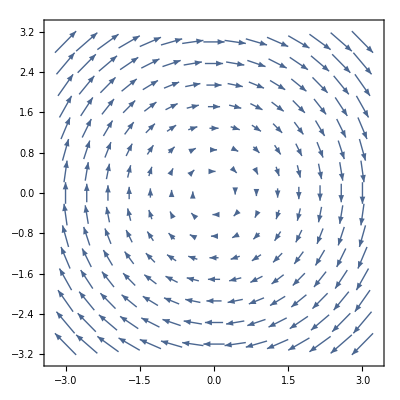

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot3D[{y,-x,z},{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[{y,-x,z},"CenterPlanes",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

### Differential Equations

```mathematica
sol = DSolveValue[y'[x]+y[x]==x, y[x],x]
```

-1+x+ⅇ^-x C[1]

```mathematica
sol/.C[1]->1
```

-1+ⅇ^-x+x

```mathematica
DSolveValue[{y'[x]+y[x]==x,y[0]==-1},y[x],x]
```

-1+x

```mathematica
NDSolveValue[{y'[x]==Cos[x^2],y[0]==0},y[x],{x,-5,5}]
```

InterpolatingFunction[…][x]

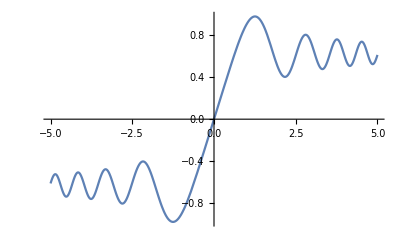

```mathematica
Plot[%,{x,-5,5}]
```

```mathematica
{xsol,ysol}=NDSolveValue[
{x'[t]==-y[t]-x[t]^2,
y'[t]==2x[t]-y[t]^3,
x[0]==y[0]==1},
{x,y},
{t,20}
]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

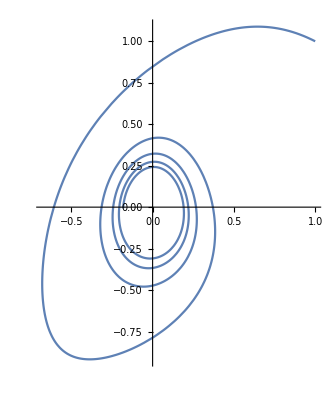

```mathematica
ParametricPlot[{xsol[t],ysol[t]},{t,0,20}]
```

### Complex Analysis

```mathematica
I^2
```

-1

```mathematica
(1+I) (2-3 I)
```

5-ⅈ

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
ExpToTrig[E^Ix]
```

Cosh[Ix]+Sinh[Ix]

```mathematica
TrigToExp[%]
```

ⅇ^Ix

```mathematica
(3+2 I)*
```

3-2 ⅈ

```mathematica
ReIm[3+2I]
```

{3,2}

```mathematica
AbsArg[(1+I)]
```

{√2,π/4}

### Matrices & Linear Algebra

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
{{a, b}, {c, d}}
```

{{a,b},{c,d}}

```mathematica
MatrixForm[%]
```

(a | b
c | d)

```mathematica
Table[x+y,{x,1,3},{y,0,2}]
```

{{1,2,3},{2,3,4},{3,4,5}}

```mathematica
MatrixForm@%
```

(1 | 2 | 3
2 | 3 | 4
3 | 4 | 5)

```mathematica
Det[{{a, b}, {c, d}}]
```

-b c+a d

```mathematica
Inverse[{{1, 1}, {0, 1}}]
```

{{1,-1},{0,1}}

```mathematica
LinearSolve[{{1, 1}, {0, 1}},{x,y}]
```

{x-y,y}

### Discrete Mathematics

```mathematica
FactorInteger[30]
```

{{2,1},{3,1},{5,1}}

```mathematica
GCD[24,60]
```

12

```mathematica
Prime[4]
```

7

```mathematica
PrimeQ[%]
```

True

```mathematica
CoprimeQ[51,15]
```

False

```mathematica
Mod[17,5]
```

2

```mathematica
Permutations[{a,b,c}]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

```mathematica
Permute[{a,b,c,d},Cycles[{{2,4},{1,3}}]]
```

{c,d,a,b}

```mathematica
PermutationOrder[Cycles[{{2,4},{1,3}}]]
```

2

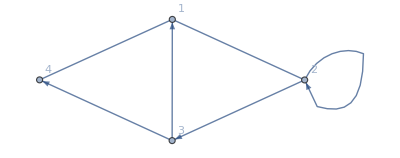

```mathematica
Graph[{1<->2,2->3,3->4,4<->1,3->1,2->2},VertexLabels->All]
```

```mathematica
FindShortestPath[%,3,2]
```

{3,1,2}

```mathematica
Entity["Graph","PappusGraph"][EntityProperty["Graph","Image"]]
```

-Graphics-

### Probability

```mathematica
5!
```

120

```mathematica
Binomial[4,2]
```

6

```mathematica
Probability[x==4,x\[Distributed]BinomialDistribution[5,1/2]]
```

5/32

```mathematica
Expectation[2x+3, x\[Distributed]NormalDistribution[]]
```

3

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

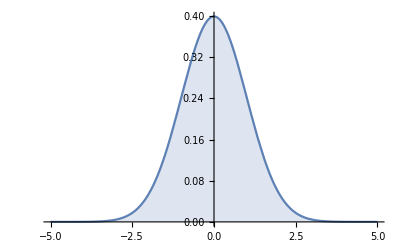

```mathematica
Plot[%,{x,-5,5},Filling->Axis]
```

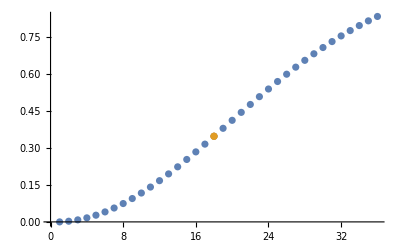

```mathematica
LinguisticAssistant
```

### Statistics

```mathematica
Mean[{1,2,4,5}]
```

3

```mathematica
Correlation[{1,3,5},{6,4,2}]
```

-1

```mathematica
StandardDeviation[PoissonDistribution[2]]
```

√2

```mathematica
Moment[{x,y,z},2]
```

1/3 (x^2+y^2+z^2)

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],t]
```

ⅇ^(t μ+(t^2 σ^2)/2)

```mathematica
RandomVariate[NormalDistribution[0,1],{5,2}]
```

{{-0.31308,-0.518974},{1.68972,1.18703},{-1.43459,0.409192},{0.225184,0.282864},{-0.520837,-0.106456}}

```mathematica
RandomVariate[NormalDistribution[0,1],{5000,2}]//Short
```

{«1»}

```mathematica
Histogram3D[%]
```

-Graphics3D-

### Data Plots & Best - Fit Curves

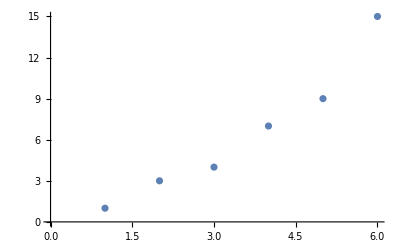

```mathematica
ListPlot[{1,3,4,7,9,15}]
```

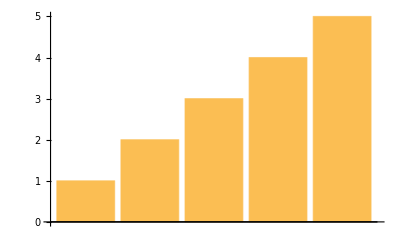

```mathematica
BarChart[{1,2,3,4,5}]
```

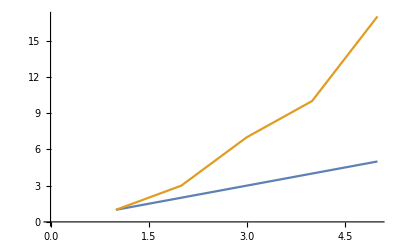

```mathematica
ListLinePlot[{{1,2,3,4,5},{1,3,7,10,17}}]
```

```mathematica
Fit[{2,3,5,7,11,13},{1,x,x^2},x]
```

0.9+0.689286 x+0.232143 x^2

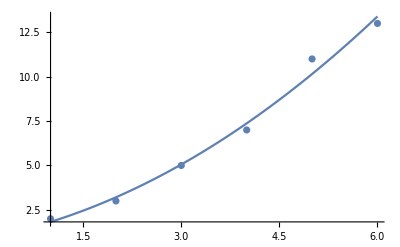

```mathematica
Show[Plot[%,{x,1,6}],ListPlot[{2,3,5,7,11,13}]]
```

### Group Theory

```mathematica
GroupElements[SymmetricGroup[2]]
```

{Cycles[{}],Cycles[{{1,2}}]}

```mathematica
GroupGenerators[SymmetricGroup[3]]
```

{Cycles[{{1,2}}],Cycles[{{1,2,3}}]}

### Math Puzzles

```mathematica
CoprimeQ[Range[1000000],1000000]//Short
```

{True,False,True,«999994»,False,True,False}

```mathematica
%/.False-> Nothing//Short
```

{True,True,True,«399994»,True,True,True}

```mathematica
Length[%]
```

400000

```mathematica
Length[CoprimeQ[Range[1000000],1000000]/.False->Nothing]
```

400000

```mathematica
∑_(i=1)^n i^2
```

1/6 n (1+n) (1+2 n)

```mathematica
∑_(i=1)^n i^k
```

HarmonicNumber[n,-k]

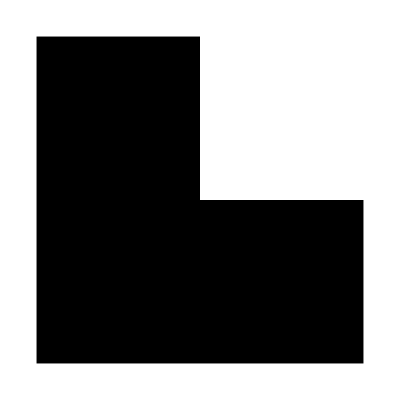
-Graphics-n

```mathematica
Labeled[Graphics[shape = 
{Rectangle[],
Rectangle[{0,1}],
Rectangle[{1,0}]}],n]
```

```mathematica
Graphics[{Scale[shape,2,{0,0}],{Yellow,shape},{Green,Translate[shape,{1,1}]},{Blue,Translate[Rotate[shape,-90 °],{0,2}]},{Red,Translate[Rotate[shape,90 °],{2,0}]}}]
```

-Graphics-

```mathematica
Graphics[{Scale[shape,3,{0,0}],{Orange,shape},{Magenta,Translate[Rotate[shape,-90 °],{0,2}]},{Green,Translate[shape,{1,1}]},{Red,Translate[Rotate[shape,90 °],{2,0}]},{Black,Translate[shape,{0,4}]},{Blue,Translate[Rotate[shape,180 °],{1,4}]},{Gray,Translate[shape,{2,2}]},{Purple,Translate[Rotate[shape,-90 °],{4,1}]},{Yellow,Translate[Rotate[shape,90 °],{4,0}]}}]
```

-Graphics-

WolframAlphaQueryResults

```mathematica
{{"number of disks", 4}}
```

```mathematica
Manipulate[Plot[Sin[f x],{x,-3,3},Filling->Axis],{f,1,5}]
```

```mathematica
Manipulate[Plot[Sin[f*x+p],{x,-3,3},
Filling->fill,
PlotStyle->color],
{f,1,5},{p,3,9},{fill,{Bottom,Top,Axis}},{color,Red}]
```

```mathematica
Manipulate[Expand[(a+b)^n],{n,1,20,1}]
```

```mathematica
TraditionalForm[(y+3)^2/((y-2) (y+5))]
```

(y+3)^2/((y-2) (y+5))

Convert existing cells to TraditionalForm using SHIFT+CMD+T:

```mathematica
(x^2-1)/(x-1)x0
```

1

### Cloud

```mathematica
CloudDeploy[Plot[Sin[x],{x,0,50}]]
```

$Failed

```mathematica
CloudDeploy[Manipulate[Plot[Sin[f x],{x,0,2 Pi}],{f,1,10}]]
```

$Failed